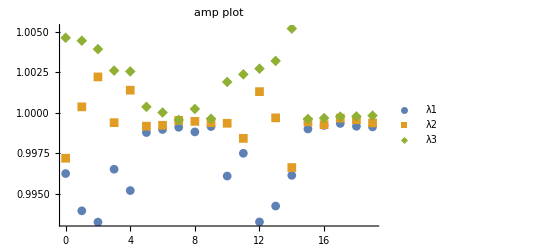

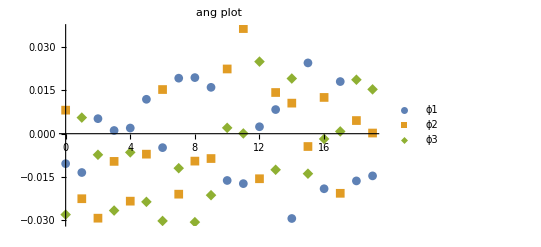

0.0680678

```mathematica
bm=Import["Google Drive/jie_programs/QHlattice/Jun5/output","Table"];
n:=Length[bm]
x=Table[bm[[i]][[1]],{i,1,n,1}];
amp1= Table[{x[[i]],bm[[i]][[2]]},{i,1,n}];
amp2= Table[{x[[i]],bm[[i]][[3]]},{i,1,n}];
amp3= Table[{x[[i]],bm[[i]][[4]]},{i,1,n}];
ang1=Table[{x[[i]],bm[[i]][[5]]},{i,1,n}];
ang2=Table[{x[[i]],bm[[i]][[6]]},{i,1,n}];
ang3=Table[{x[[i]],bm[[i]][[7]]},{i,1,n}];

ListPlot[{amp1, amp2, amp3},PlotLegends->{"λ1","λ2", "λ3"},PlotMarkers->Automatic, PlotLabel->"amp plot"]
ListPlot[{ang1, ang2, ang3},PlotLegends->{"ϕ1","ϕ2", "ϕ3"},PlotMarkers->Automatic, PlotLabel->"ang plot"]
13*0.0025/3*π*2
```

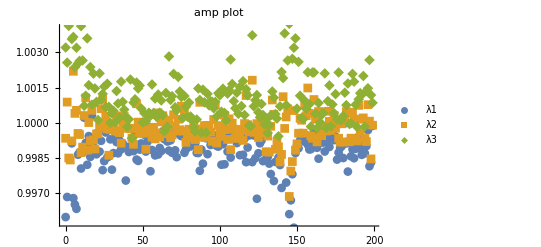

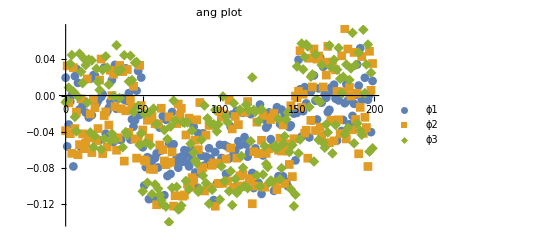

6.80678

```mathematica
bm=Import["Google Drive/jie_programs/QHlattice/Jun5/output2","Table"];
n:=Length[bm]
x=Table[bm[[i]][[1]],{i,1,n,1}];
amp1= Table[{x[[i]],bm[[i]][[2]]},{i,1,n}];
amp2= Table[{x[[i]],bm[[i]][[3]]},{i,1,n}];
amp3= Table[{x[[i]],bm[[i]][[4]]},{i,1,n}];
ang1=Table[{x[[i]],bm[[i]][[5]]},{i,1,n}];
ang2=Table[{x[[i]],bm[[i]][[6]]},{i,1,n}];
ang3=Table[{x[[i]],bm[[i]][[7]]},{i,1,n}];

ListPlot[{amp1, amp2, amp3},PlotLegends->{"λ1","λ2", "λ3"},PlotMarkers->Automatic, PlotLabel->"amp plot"]
ListPlot[{ang1, ang2, ang3},PlotLegends->{"ϕ1","ϕ2", "ϕ3"},PlotMarkers->Automatic, PlotLabel->"ang plot"]
13*0.25/3*π*2
```